# Matematyka podstawy

## Operacje matematyczne

```mathematica
1+2
```

3

```mathematica
2^3
```

8

```mathematica
N[Sqrt[3],10]
```

1.732050808

```mathematica
Power[√67,0.5]
```

```mathematica
2.861005552576305
```

2.86101

```mathematica
%*Pi
```

Overflow[]

```mathematica
%^(%^%)
```

1.72839×10^9

```mathematica
ⅇ^4
```

ⅇ^4

```mathematica
Abs[I]
```

1

```mathematica
a=5
b=6
a+b
```

5

6

```mathematica
11
7 4
```

11

```mathematica
28
```

28

```mathematica
FactorInteger[28]
```

{{2,2},{7,1}}

```mathematica
N[Cos[a Degree]]
```

0.996195

```mathematica
Exp[b]
```

ⅇ^6

```mathematica
N[Out[10]]
```

0.996195

```mathematica
f[x_]:=x^2-2
f[3]
```

7

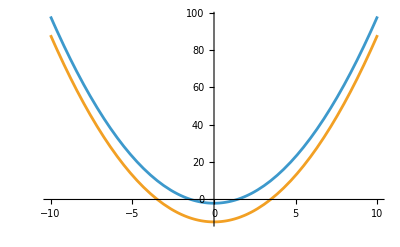

```mathematica
Plot[{f[x],g[x,2]},{x,-10,10}]
```

```mathematica
g[x_,y_]:=x^2-3 y^2
```

```mathematica
D[Tan[x],x]
```

Sec[x]^2

```mathematica
D[g[x,y],y]
```

-6 y

```mathematica
Integrate[f[x],x]
Integrate[f[x],{x,-1,1}]
```

-2 x+x^3/3

-10/3

```mathematica
l={1,3,0,6,7}
Length[l]
l[[3]]
```

{1,3,0,6,7}

5

0

# Równania

```mathematica
sol=Solve[x^2+2x-3==0,x]
sol[[1]]
sol[[2]]
```

{{x→-3},{x→1}}

{x→-3}

{x→1}

```mathematica
{x,x^2+2x-3}/.sol
```

```mathematica
{{-3,0},{1,0}}
```

{{-3,0},{1,0}}

```mathematica
Flatten[Values[sol]]
```

{-3,1}

{{x→ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]}}

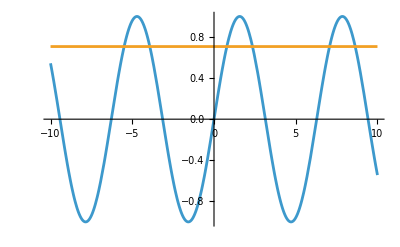

```mathematica
Solve[Sin[x]== (√2)/2,x]
p1=Plot[{Sin[x],(√2)/2},{x,-10,10}]
```

```mathematica
Solve[D[f[x],x]==0]
```

{{x→0}}

```mathematica
pcos[x_]=Normal[Series[Cos[x],{x,0,4}]]
```

1-x^2/2+x^4/24

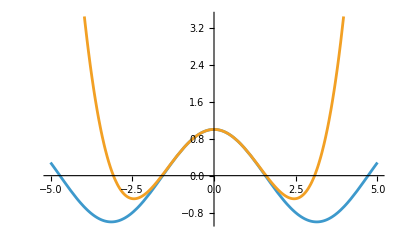

```mathematica
Plot[{Cos[x],pcos[x]},{x,-5,5}]
```

```mathematica
Limit[Sin[x]/x,{x -> 0},Direction->"FromBelow"]
```

1

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

# Zadanie przebieg zmiennosci f-cji

```mathematica
z[x_]=x^3/(1-x^2)
```

x^3/(1-x^2)

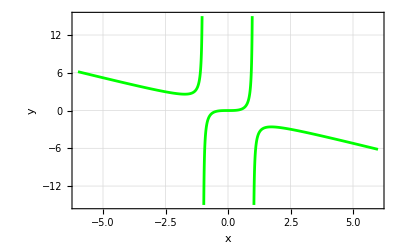

```mathematica
p1=Plot[z[x],{x,-6,6},Frame->True,GridLines->Automatic,PlotStyle->Green,PlotRange->{{-6,6},{-15,15}},FrameLabel->{"x","y"}]
```

```mathematica
zero ={x,0}/. Solve[z[x]==0,x]
```

{{0,0},{0,0},{0,0}}

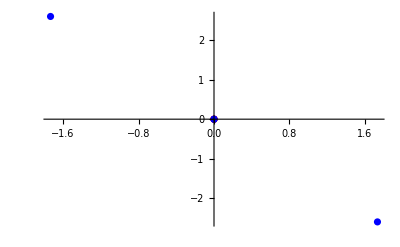

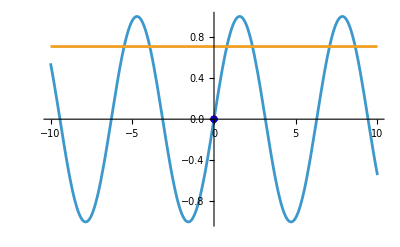

```mathematica
p2=ListPlot[{zero,extrema},PlotStyle->{{Red,Large},{Blue,Large}}]
Show[p1,p2]
```

```mathematica
extrema = {x,z[x]}/.Solve[D[z[x],x]==0 && D[f[x],{x,2}]!=0,x]
```

{{0,0},{0,0},{-√3,(3 √3)/2},{√3,-(3 √3)/2}}